```mathematica
An example due to Joao Penedones and Pedro Vieira, code of David Simmons-Duffin
```

```mathematica
k[β_,z_]:=k[β,z]=z^(β/2)Hypergeometric2F1[β/2,β/2,β,z];
g[Δ_,L_][z_,zb_]:=k[Δ+L,z]k[Δ-L,zb]+k[Δ+L,zb]k[Δ-L,z];
H[Δϕ_,Δ_,L_][z_,zb_]:=1/((z zb)^Δϕ-((1-z)(1-zb))^Δϕ)(((1-z)(1-zb))^Δϕ g[Δ,L][z,zb]-(z zb)^Δϕ g[Δ,L][1-z,1-zb]);
```

```mathematica
vector[h_]:={h[0.5,0.6]-h[0.5,0.333],h[0.5,0.6]-h[0.333,0.25]};

normalizedVector[Δϕ_,Δ_,L_]:=Module[{
v=vector[H[Δϕ,Δ,L]],
λ=If[L>0,1-L/20,1-Δ/20]
},
λ v/Norm[v]
];
```

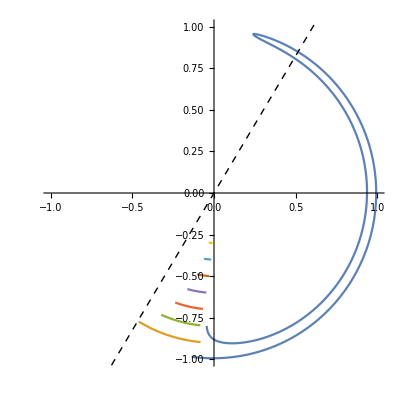

```mathematica
Module[{
Δϕ=0.125,
τmin=0.01,
τmax=4,
Lmax=14,
ΔscalarMin=0.1 (* this is the parameter to vary to shave off parts of the scalar curve *),
stressTensorVector,
blockVectors
},
stressTensorVector=normalizedVector[Δϕ,2,2];
blockVectors=Table[
normalizedVector[Δϕ,τ+L,L],
{L,0,Lmax,2},
{τ,If[L==0,ΔscalarMin,τmin],τmax,If[L==0,1/1000,1/10]}
];
Show[
ListPlot[
blockVectors,
PlotRange->{{-1,1},{-1,1}},
AspectRatio-> 1,
Joined-> True,
InterpolationOrder-> 4
],
Graphics[{
Dashed,
Line[{2 stressTensorVector,-2 stressTensorVector}]}
]
]
]
```